# Centrifuge problem

The solution below is using an exhaustive method, that is, we check every possible point in the solution space sequentially in order to determine if it is indeed a solution.

This version includes improvements in the function definitions so they can be right composed properly. For some unexpected reasons, this vastly reduces the computation times.

## Functions

## Find roots

### Hand-made function

```mathematica
MyFindRoots[z_,n_]:=Module[{roots,r,angle},
roots=ConstantArray[0,n];
For[k=0,k<n,k++,{
r=Abs[z],
angle=Arg[z],
r=r^(1/n),
roots[[k+1]]=r*Exp[I*(angle+2*Pi*k)/n]
}];
roots
]
```

### Native-based function

```mathematica
MyFindRootsNative[z_,n_]:=Solve[x^n==z,x][[All,1,2]]
```

### Summary

```mathematica
AbsoluteTiming[MyFindRoots[1+I,100000];]
AbsoluteTiming[MyFindRoots[1,100000];]
```

{1.40589,Null}

{0.642397,Null}

```mathematica
AbsoluteTiming[MyFindRootsNative[1+I,100000];]
AbsoluteTiming[MyFindRootsNative[1,100000];]
```

{1.19682,Null}

{0.495344,Null}

For arbitrary complex numbers, my hand-made method seems to be slightly faster, as it goes straight to business. I guess the Solve[] function is slower because it probably uses a different, more general method, while my method is a very simple algorithm built specifically for this task.

However, for our problem, which is “rotating” a number (1; although any complex number would work) on the complex plane, the native method using Solve[] destroys my method by taking half the time.

### Selected method

From this we can easily select which function to use in the calculations.

```mathematica
UsedFindRoots[z_,n_]:=MyFindRootsNative[z,n]
```

## Solver function

### Sort/reorder solutions clockwise

```mathematica
SortSetClockwise[set_]:=Module[{angles,order},
angles=Map[Arg,set];
order=Ordering[angles,All, NumericalOrder];
angles=angles[[order]];
Map[Exp,I*Pi *Rationalize[N[angles]/Pi]]
]
```

This step is probably the most important one to minimize calculations. Since we’ll be comparing solutions in set form as a whole, we need to make sure they follow a specific structure. An alternative would be using the Sort[] function, but it doesn’t seem to work properly with numbers in exponential form.

### Classify solutions by size

The purpose of this step is to classify solutions by k (that is, by the amount of test tubes). This is important to make sure at no point we compare {-i, 1, i, -1} with {1, -1}.

```mathematica
ClassifyCentrifugeSols[solutions_]:=Module[{classMat,classVect,roots,subsets,subset,epsilon,n,curr,next,i},
n=Length[solutions[[1]]];
subsets=Sort[solutions[[2]]];
roots=solutions[[1]];
epsilon=Power[10,-15];
classMat={};
classVect={};
(*Main loop*)
For[i=1,i≤Length[subsets],i++,{
subset=subsets[[i]],
curr=Length[subset];
(*Check length of next element*)
If[i+1<=Length[subsets],
next=Length[subsets[[i+1]]],
next=0
];
(*Append subset to vector*)
classVect=Append[classVect,SortSetClockwise[subset]];
(*Append subsets to matrix*)
If[next!=Length[subset] && Length[classVect]>0,
classMat=Append[classMat,{curr,classVect}];
classVect={};
];
}];
(*Return*)
{roots,classMat}
]
```

### Solution finder

```mathematica
FindCentrifugeSols[n_]:=Module[{solutions,roots,subsets,subset,total, epsilon,i},
roots=UsedFindRoots[1,n];
subsets=Subsets[roots,n];
epsilon=Power[10,-15];
solutions={};
(*Main loop*)
For[i=1,i≤Length[subsets],i++,{
subset=subsets[[i]],
total=Total[subset],
If[Abs[N[total]] < epsilon,
solutions=Append[solutions,SortSetClockwise[subset]]
]
}];
(*Return*)
ClassifyCentrifugeSols[{roots,solutions}]
]
```

#### Example

```mathematica
FindCentrifugeSols[4]
```

{{-1,-ⅈ,ⅈ,1},{{0,{{}}},{2,{{-ⅈ,ⅈ},{1,-1}}},{4,{{-ⅈ,1,ⅈ,-1}}}}}

## Reduce solutions

### Rotation function

```mathematica
RotateSol[n_,k_,sol_]:=sol*Exp[I*(2*Pi*k)/n]
```

This function simply applies a rotation of (2*Pi*k)/n to a complex number. This is essential to reduce the found solutions to unique solutions under a rotation symmetry.

### Reduce solutions under rotations

```mathematica
ReduceRotations[solutions_]:=Module[{subSols,uniqueSubSols,uniqueSols,n, numSubSets,rotatedSol,rotatedSols,tempSol,element,i},
n=Length[solutions[[1]]];
numSubSets=Length[solutions[[2]]];
uniqueSols={};
(*Iterate over each subset size*)
For[i=1,i≤numSubSets,i++,
uniqueSubSols={};
subSols=solutions[[2]][[i]][[2]];
(*Loop over solution sub-space*)
For[element=1,element≤Length[subSols],element++,
rotatedSols={};
tempSol=subSols[[element]];
tempSol=SortSetClockwise[tempSol];
(*Rotate one solution*)
For[k=0,k<n,k++,
rotatedSol=RotateSol[n,k,tempSol];
rotatedSol=SortSetClockwise[rotatedSol];
rotatedSols=Append[rotatedSols,rotatedSol]
];
(*Add to list of unique solutions*)
If[Length[Intersection[uniqueSubSols,rotatedSols]]==0,
uniqueSubSols=Append[uniqueSubSols,tempSol];
]
];
uniqueSols=Append[uniqueSols,{solutions[[2]][[i]][[1]],uniqueSubSols}];
];
(*Return*)
{solutions[[1]],uniqueSols}
]
```

#### Examples

```mathematica
4 //FindCentrifugeSols
```

{{-1,-ⅈ,ⅈ,1},{{0,{{}}},{2,{{-ⅈ,ⅈ},{1,-1}}},{4,{{-ⅈ,1,ⅈ,-1}}}}}

```mathematica
4 //FindCentrifugeSols // ReduceRotations
```

{{-1,-ⅈ,ⅈ,1},{{0,{{}}},{2,{{-ⅈ,ⅈ}}},{4,{{-ⅈ,1,ⅈ,-1}}}}}

### Reflection function

```mathematica
ReflectSol[sol_]:=-Conjugate[sol]
```

### Reduce solutions under reflections

```mathematica
ReduceReflections[solutions_]:=Module[{subSols,uniqueSubSols,uniqueSols,n, numSubSets,rotatedSol,rotatedSols,tempSolSrc,tempSol,element,i},
n=Length[solutions[[1]]];
numSubSets=Length[solutions[[2]]];
uniqueSols={};
(*Iterate over each subset size*)
For[i=1,i≤numSubSets,i++,
uniqueSubSols={};
subSols=solutions[[2]][[i]][[2]];
(*Loop over solution sub-space*)
For[element=1,element≤Length[subSols],element++,
tempSolSrc=subSols[[element]];
rotatedSols={tempSolSrc};
tempSol=ReflectSol[tempSolSrc];
tempSol=SortSetClockwise[tempSol];
(*Rotate one solution*)
For[k=0,k<n,k++,
rotatedSol=RotateSol[n,k,tempSol];
rotatedSol=SortSetClockwise[rotatedSol];
rotatedSols=Append[rotatedSols,rotatedSol]
];
(*Add to list of unique solutions*)
If[Length[Intersection[uniqueSubSols,rotatedSols]]==0,
uniqueSubSols=Append[uniqueSubSols,tempSolSrc];
]
];
uniqueSols=Append[uniqueSols,{solutions[[2]][[i]][[1]],uniqueSubSols}];
];
(*Return*)
{solutions[[1]],uniqueSols}
]
```

#### Examples

```mathematica
Sols12Rot:=12 //FindCentrifugeSols // ReduceRotations
Sols12Ref:=12 //FindCentrifugeSols // ReduceRotations//ReduceReflections
```

```mathematica
Roots12 :=Sols12Rot[[1]]
```

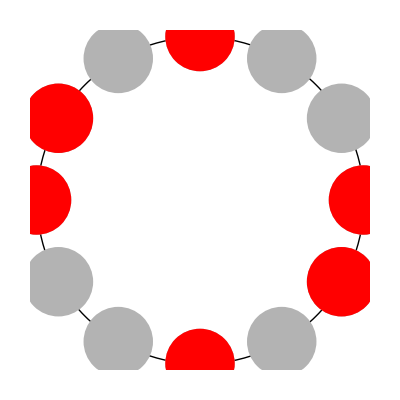
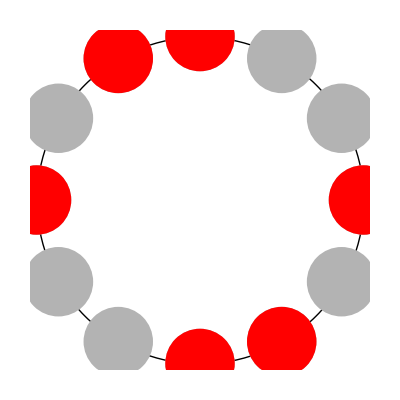
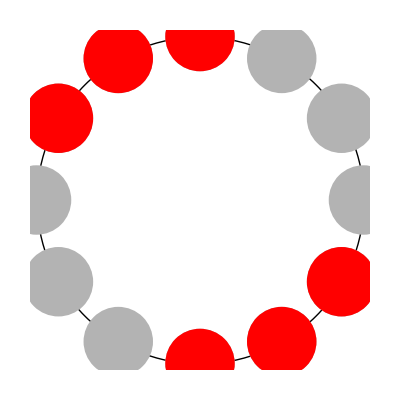
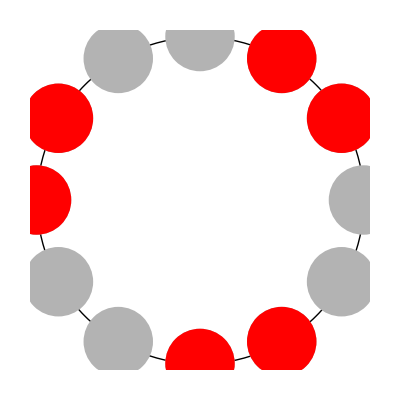
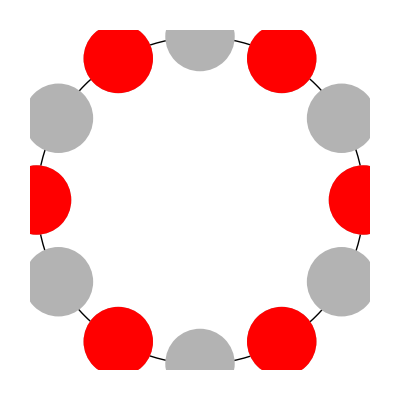

```mathematica
Map[PlotCentrifuge[#,Roots12]&,Sols12Rot[[2]][[6]][[2]]]
```

```mathematica
Map[PlotCentrifuge[#,Roots12]&,Sols12Ref[[2]][[6]][[2]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

As we can see, this effectively removes the

## Drawing functions

### Auxiliary plotting functions

```mathematica
PlotCentrifuge[z_,roots_]:=Module[{},
PlotComplexBase[roots]:=ListPlot[
{Re[#],Im[#]}&/@roots,
AxesOrigin->{0,0},
Axes->False,
PlotRange->{{-1.2,1.2},{-1.2,1.2}},
ImagePadding->0,
AspectRatio->1,
Frame->False,
FrameLabel->{{Im,None},{Re,None}},
PlotStyle->Directive[GrayLevel[0.7],PointSize[0.2]]
];
PlotComplex[z]:=ListPlot[
{Re[#],Im[#]}&/@z,
AxesOrigin->{0,0},
Axes->False,
PlotRange->{{-1.2,1.2},{-1.2,1.2}},
ImagePadding->0,
AspectRatio->1,
Frame->False,
FrameLabel->{{Im,None},{Re,None}},
PlotStyle->Directive[Red,PointSize[.2]]
];
(*Return*)
Show[
Graphics@Circle[{0,0},1],
PlotComplexBase[roots],
PlotComplex[z],
ImageSize->Tiny
]
]
```

### Draw solutions

```mathematica
DrawCentrifugeSols[solutions_]:=Module[{numSubSets,roots,n,solsTable,i},
n=Length[solutions[[1]]];
roots=solutions[[1]];
numSubSets=Length[solutions[[2]]];
solsTable={{"Elements","Representation"}};
(*Loop over subsets*)
For[i=1,i≤numSubSets,i++,
solsTable=Append[
solsTable,
{solutions[[2]][[i]][[1]],
PlotCentrifuge[#,roots]&/@solutions[[2]][[i]][[2]]}
]
];
Print["Roots for ",n, " holes: ",roots];
Print["Solutions:"];
(*Return*)
Grid[solsTable,
Background->{None,{Lighter[Yellow,.9],None}},
Alignment->{{Center,Left}}, 
Dividers->{All,All}
]
]
```

#### Examples

Roots for 4 holes: {-1,-ⅈ,ⅈ,1}

Solutions:

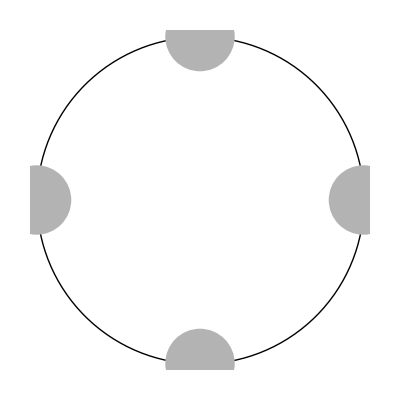
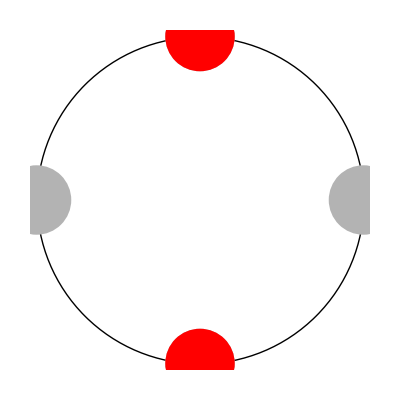
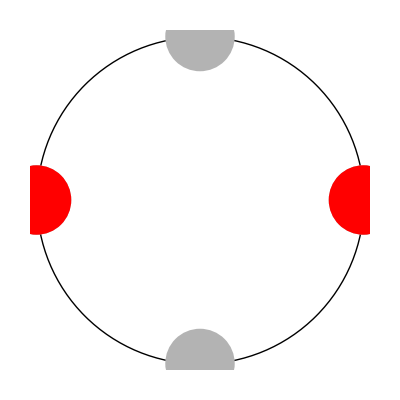
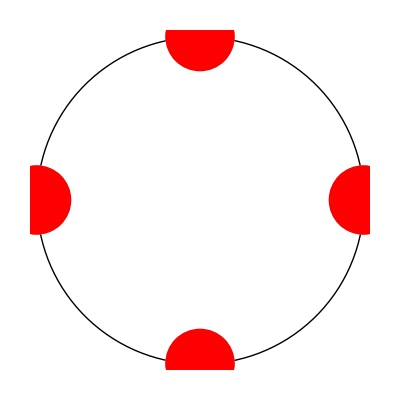
Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-,-Graphics-}
4 | {-Graphics-}

```mathematica
4 //FindCentrifugeSols // DrawCentrifugeSols
```

```mathematica
4 //FindCentrifugeSols //ReduceRotations// DrawCentrifugeSols
```

Roots for 4 holes: {-1,-ⅈ,ⅈ,1}

Solutions:

Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-}
4 | {-Graphics-}

## Solutions and examples

## n = 4

```mathematica
AbsoluteTiming[4//FindCentrifugeSols //ReduceRotations]
AbsoluteTiming[4//FindCentrifugeSols //ReduceRotations// DrawCentrifugeSols]
```

{0.001944,{{-1,-ⅈ,ⅈ,1},{{0,{{}}},{2,{{-ⅈ,ⅈ}}},{4,{{-ⅈ,1,ⅈ,-1}}}}}}

Roots for 4 holes: {-1,-ⅈ,ⅈ,1}

Solutions:

{0.096857,Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-}
4 | {-Graphics-}}

## n = 12

{0.340885,{{-1,-ⅈ,ⅈ,1,-(-1)^(1/6),(-1)^(1/6),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(5/6),(-1)^(5/6)},{{0,{{}}},{2,{{-ⅈ,ⅈ}}},{3,{{-ⅈ,ⅇ^((ⅈ π)/6),ⅇ^((5 ⅈ π)/6)}}},{4,{{-ⅈ,1,ⅈ,-1},{-ⅈ,ⅇ^(-(ⅈ π)/6),ⅈ,ⅇ^((5 ⅈ π)/6)},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3)}}},{5,{{-ⅈ,1,ⅇ^((ⅈ π)/6),ⅇ^((5 ⅈ π)/6),-1}}},{6,{{-ⅈ,ⅇ^(-(ⅈ π)/6),1,ⅈ,ⅇ^((5 ⅈ π)/6),-1},{-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅈ,ⅇ^((2 ⅈ π)/3),-1},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6)},{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),-1}}},{7,{{-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1}}},{8,{{-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((5 ⅈ π)/6),-1},{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),-1}}},{9,{{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1}}},{10,{{ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1}}},{12,{{ⅇ^(-(5 ⅈ π)/6),ⅇ^(-(2 ⅈ π)/3),-ⅈ,ⅇ^(-(ⅈ π)/3),ⅇ^(-(ⅈ π)/6),1,ⅇ^((ⅈ π)/6),ⅇ^((ⅈ π)/3),ⅈ,ⅇ^((2 ⅈ π)/3),ⅇ^((5 ⅈ π)/6),-1}}}}}}

Roots for 12 holes: {-1,-ⅈ,ⅈ,1,-(-1)^(1/6),(-1)^(1/6),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(5/6),(-1)^(5/6)}

Solutions:

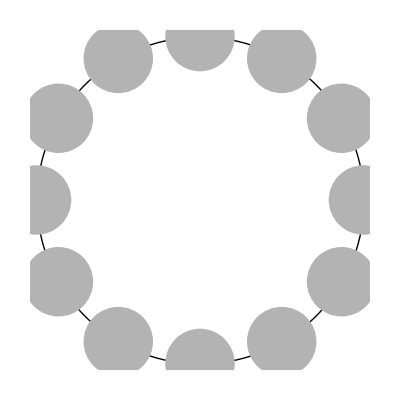
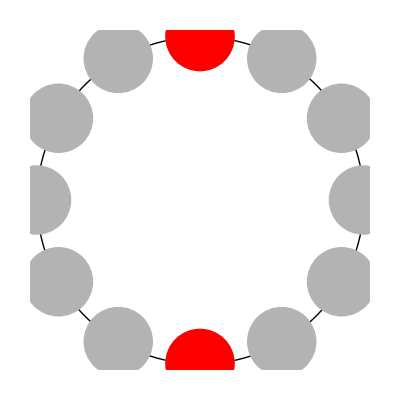
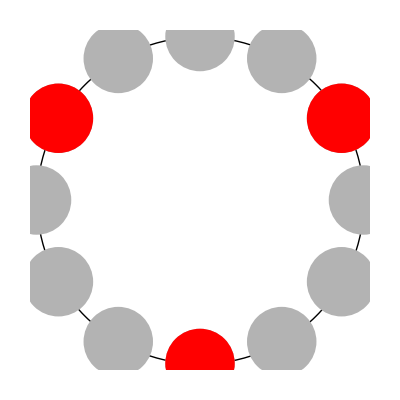
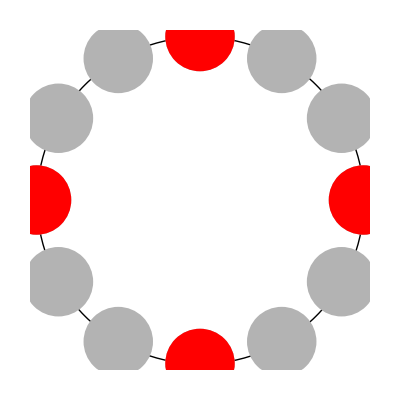
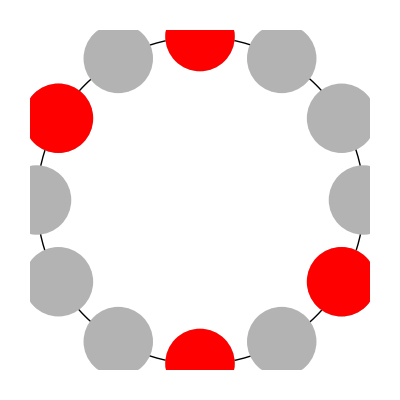
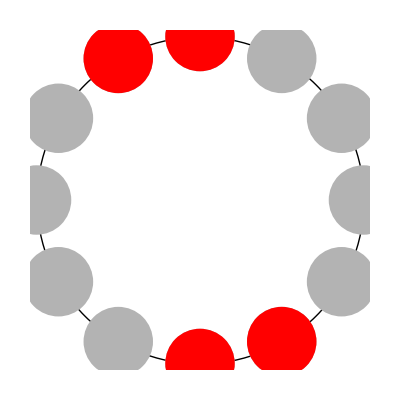
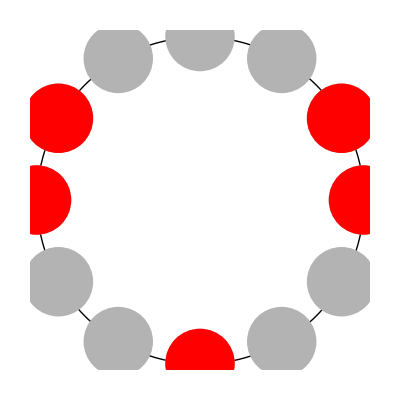
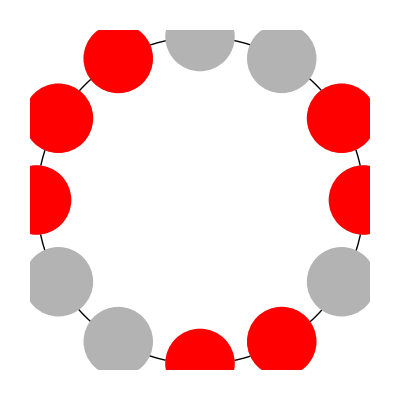
{0.727719,Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-}
3 | {-Graphics-}
4 | {-Graphics-,-Graphics-,-Graphics-}
5 | {-Graphics-}
6 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
7 | {-Graphics-}
8 | {-Graphics-,-Graphics-,-Graphics-}
9 | {-Graphics-}
10 | {-Graphics-}
12 | {-Graphics-}}

Roots for 12 holes: {-1,-ⅈ,ⅈ,1,-(-1)^(1/6),(-1)^(1/6),-(-1)^(1/3),(-1)^(1/3),-(-1)^(2/3),(-1)^(2/3),-(-1)^(5/6),(-1)^(5/6)}

Solutions:

{0.971946,Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-}
3 | {-Graphics-}
4 | {-Graphics-,-Graphics-,-Graphics-}
5 | {-Graphics-}
6 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-}
7 | {-Graphics-}
8 | {-Graphics-,-Graphics-,-Graphics-}
9 | {-Graphics-}
10 | {-Graphics-}
12 | {-Graphics-}}

```mathematica
AbsoluteTiming[12//FindCentrifugeSols //ReduceRotations]
AbsoluteTiming[12//FindCentrifugeSols //ReduceRotations// DrawCentrifugeSols]
AbsoluteTiming[12//FindCentrifugeSols //ReduceRotations//ReduceReflections// DrawCentrifugeSols]
```

## n = 24

The refactoring of the functions allows to calculate solutions for larger numbers of holes, 24 being of special interest.

Roots for 24 holes: {-1,-ⅈ,ⅈ,1,-(-1)^(1/12),(-1)^(1/12),-(-1)^(1/6),(-1)^(1/6),-(-1)^(1/4),(-1)^(1/4),-(-1)^(1/3),(-1)^(1/3),-(-1)^(5/12),(-1)^(5/12),-(-1)^(7/12),(-1)^(7/12),-(-1)^(2/3),(-1)^(2/3),-(-1)^(3/4),(-1)^(3/4),-(-1)^(5/6),(-1)^(5/6),-(-1)^(11/12),(-1)^(11/12)}

Solutions:

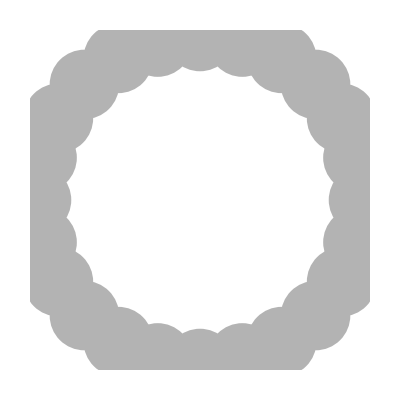
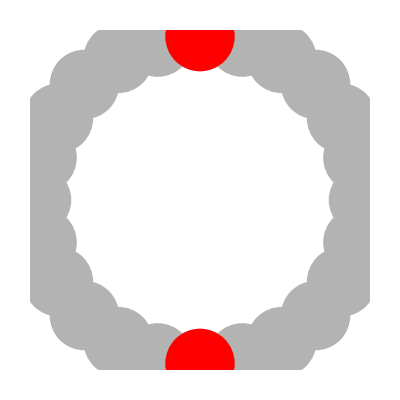
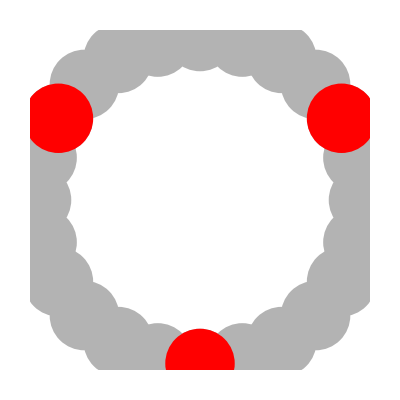
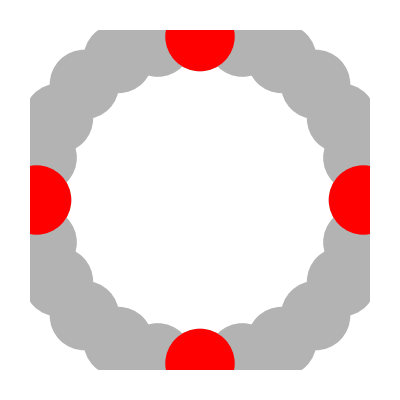
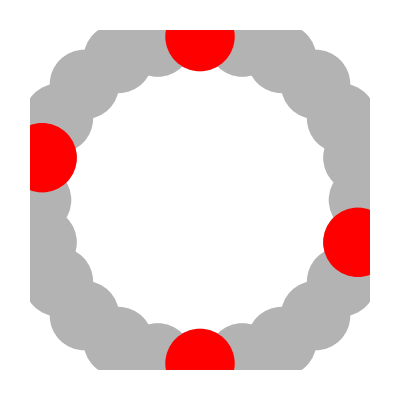
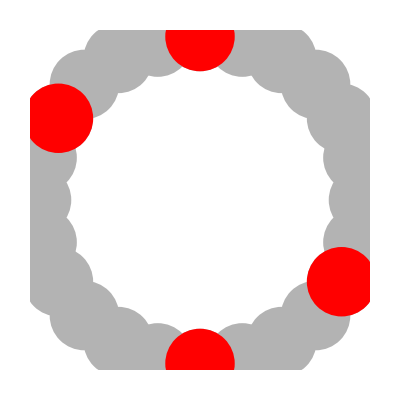
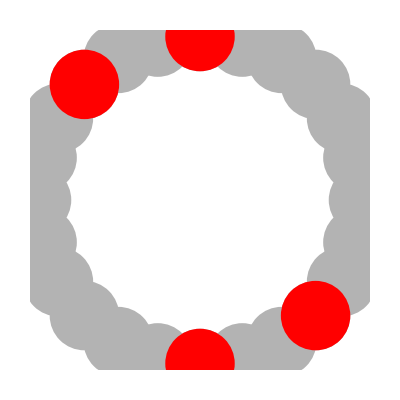
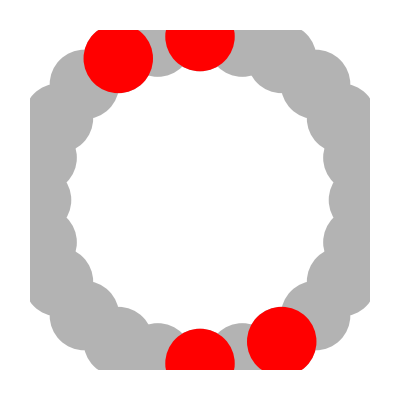
{333.758,Elements | Representation
0 | {-Graphics-}
2 | {-Graphics-}
3 | {-Graphics-}
4 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
5 | {-Graphics-,-Graphics-,-Graphics-}
6 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
7 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
8 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
9 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
10 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
11 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
12 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
13 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
14 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
15 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
16 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
17 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
18 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
19 | {-Graphics-,-Graphics-,-Graphics-}
20 | {-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
21 | {-Graphics-}
22 | {-Graphics-}
24 | {-Graphics-}}

```mathematica
AbsoluteTiming[24//FindCentrifugeSols //ReduceRotations// DrawCentrifugeSols]
```